w (ζ)

```mathematica
a=-3*ⅈ;
a1=ⅈ*Log[ζ-a];
a2=-ⅈ*Log[1/ζ-Conjugate[a]];
w=Simplify[(a1+a2)/.ζ->-ⅈ]
```

-π

dw/d  ζ * dζ / dz

```mathematica
Sigma[θ_]:=Simplify[Abs[D[(a1+a2), ζ]/.ζ->ⅇ^(ⅈ*θ)]/Sin[θ]];Sigmaζ[θ_]:=Simplify[Abs[D[(a1+a2), ζ]/.ζ->ⅇ^(ⅈ*θ)]];Sigma[θ]
Sigmaζ[θ]
```

Abs[ⅇ^(-2 ⅈ θ)/(-3 ⅈ+ⅇ^(-ⅈ θ))+1/(3 ⅈ+ⅇ^(ⅈ θ))] Csc[θ]

Abs[ⅇ^(-2 ⅈ θ)/(-3 ⅈ+ⅇ^(-ⅈ θ))+1/(3 ⅈ+ⅇ^(ⅈ θ))]

```mathematica
Sigma[θ]^2/.θ->π/2
```

1/4

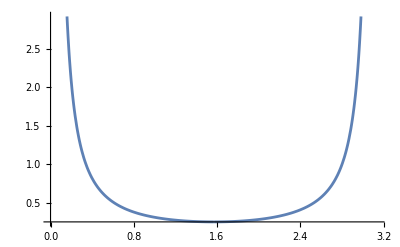

```mathematica
Plot[Sigma[θ]^2,{θ,0,π}]
```

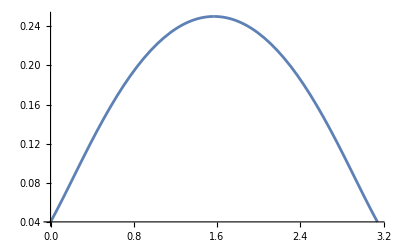

```mathematica
Plot[Sigmaζ[θ]^2,{θ,0,π}]
```

Check  deriv z and ζ work, really same, OMG

```mathematica
dz=ζ/2+1/(2ζ);
cz=Abs[1/D[dz, ζ]/.ζ->ⅇ^(ⅈ*theta)]
```

1/Abs[1/2-1/2 ⅇ^(-2 ⅈ theta)]

```mathematica
dζ=z-√(z^2-1);
cζ=Abs[D[dζ, z]/.z->Cos[theta]]
```

Abs[1-Cos[theta]/(√(-1+Cos[theta]^2))]

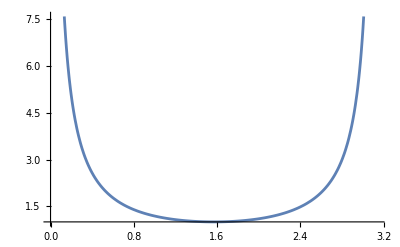

```mathematica
Plot[cz,{theta,0,π}]
```

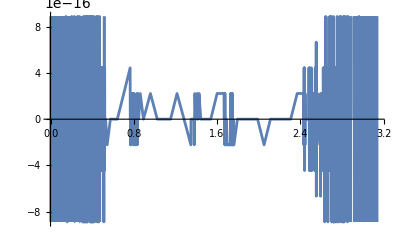

```mathematica
Plot[cζ-cz,{theta,0,π}]
```

```mathematica
wz=ⅈ*(Log[z+√(z^2-1)-a]-Log[1/(z+√(z^2-1))+a]);
```

```mathematica
w1=ⅈ*Log[z+√(z^2-1)-Subscript[ζ, 0]];
```

```mathematica
Simplify[D[w1, z]]
```

(ⅈ (1+z/(√(-1+z^2))))/(z+√(-1+z^2)-ζ_0)

```mathematica
Abs[Expand[D[wz, z]]/.z->x]
```

Abs[ⅈ/(3 ⅈ+x+√(-1+x^2))+(ⅈ x)/(√(-1+x^2) (3 ⅈ+x+√(-1+x^2)))+ⅈ/((x+√(-1+x^2))^2 (-3 ⅈ+1/(x+√(-1+x^2))))+(ⅈ x)/(√(-1+x^2) (x+√(-1+x^2))^2 (-3 ⅈ+1/(x+√(-1+x^2))))]

```mathematica
wζ=ⅈ*(Log[ζ-a]-Log[ζ+a]);
```

```mathematica
Abs[Simplify[D[wζ, ζ]*(2*ζ^2)/(ζ^2-1)/.ζ->(z+√(1-z^2))]]
```

Abs[(3+6 z √(1-z^2))/(z^2-z^4+5 z √(1-z^2))]

```mathematica
Abs[Simplify[ζ^2-1/.ζ->(x+√(1-x^2))]]
```

2 Abs[x √(1-x^2)]

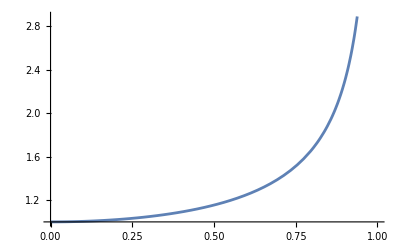

```mathematica
Plot[1/(√(1-x^2)),{x,0,1}]
```

```mathematica
N[∫_0.0001^(1-0.0001) sⅆx]
```

1.04189

```mathematica
wzt=ⅈ*(Log[z+√(z^2-1)-a])
```

ⅈ Log[3 ⅈ+z+√(-1+z^2)]

```mathematica
Simplify[D[wzt, z]]
```

(ⅈ (1+z/(√(-1+z^2))))/(3 ⅈ+z+√(-1+z^2))

```mathematica
wζt=ⅈ*(Log[ζ-a]);
```

```mathematica
Simplify[(2*ζ^2)/(ζ^2-1)/.ζ->(z+√(z^2-1))]
```

((z+√(-1+z^2))^2)/(-1+z^2+z √(-1+z^2))

```mathematica
Simplify[D[wζt, ζ]]
```

ⅈ/(3 ⅈ+ζ)

```mathematica
1/(√(1-x^2))*1/(5+4*√(1-x^2))/.x->0
```

1/9

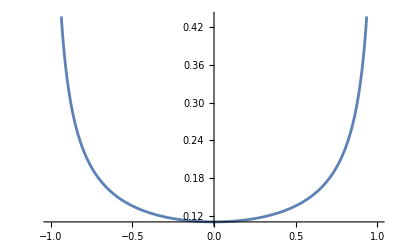

```mathematica
Plot[1/(√(1-x^2))*1/(5+4*√(1-x^2)),{x,-1,1}]
```

```mathematica
s2=(1/(√(1-x^2))*1/(5+4*√(1-x^2)))^2
```

1/((1-x^2) (5+4 √(1-x^2))^2)

```mathematica
Series[s2,{x,0,2}]
```

1/81+(13 x^2)/729+O[x]^3

```mathematica
Expand[(5+4 √(1-x^2))^2]
```

41-16 x^2+40 √(1-x^2)

```mathematica
s2a=1/(41-16 x^2+40 √(1-x^2))
```

1/(41-16 x^2+40 √(1-x^2))

```mathematica
wz=Series[s2,{x,0,2}]
```

1/81+(13 x^2)/729+O[x]^3

```mathematica
D[s2,{x,1}]
```

(8 x)/((1-x^2)^(3/2) (5+4 √(1-x^2))^3)+(2 x)/((1-x^2)^2 (5+4 √(1-x^2))^2)

```mathematica
D[s2a,{x,1}]
```

-(-32 x-(40 x)/(√(1-x^2)))/((1-x^2) (41-16 x^2+40 √(1-x^2))^2)+(2 x)/((1-x^2)^2 (41-16 x^2+40 √(1-x^2)))

```mathematica
x=0 best fit
```

```mathematica
D[s2,{x,2}]/.x->0
```

26/729

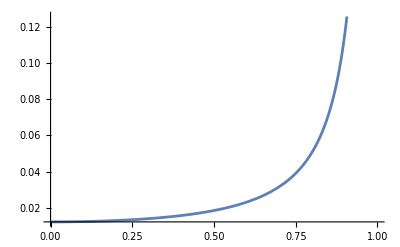

```mathematica
Plot[s2a,{x,0,1}]
```

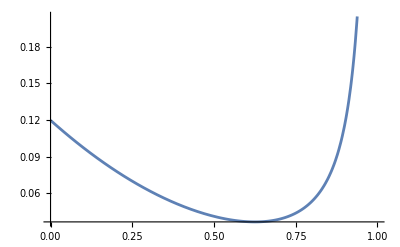

```mathematica
Plot[-1/(50 (x-1))+(4 √2 √(1-x))/(125 √(-1+x) √(x-1))+217/2500-(281 (√2 √(1-x)) √(x-1))/(3125 √(-1+x))-(4221 (x-1))/25000+(87379 √(1-x) (x-1)^(3/2))/(312500 √2 √(-1+x))+(1338633 (x-1)^2)/6250000,{x,0,1}]
```

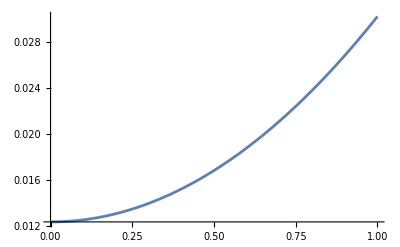

```mathematica
Plot[1/81+(13 x^2)/729,{x,0,1}]
```

```mathematica
p=1;hxx=p-1/2*(1/81+(13 x^2)/729);
```

```mathematica
hx=c1*∫hxxⅆx+k1
```

k1+(c1 (1449 x-(13 x^3)/3))/1458

```mathematica
hx/.x->1
```

(2167 c1)/2187+k1

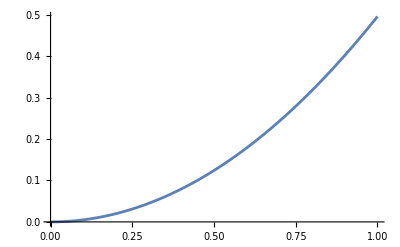

```mathematica
Plot[h,{x,0,1}]
```

```mathematica
b=.;
```

```mathematica
h=-b* x^4+b x^2-x^2+1
```

1-x^2+b x^2-b x^4

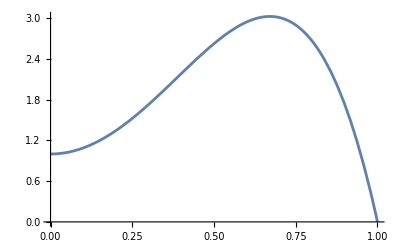

```mathematica
Plot[-b* x^4+b x^2-x^2+1/.b->10,{x,0,1}]
```

```mathematica
Plot3D[h,{x,0,1},{b,1,50}]
```

-Graphics3D-

```mathematica
Plot3D[-b* x^4+b x^2-x^2+1,{x,0,1},{b,1,50},AxesLabel->{"x","b","y"}]
```

-Graphics3D-

no  charge  below

```mathematica
so=(1/(√(1-x^2)))^2;
```

```mathematica
ho=P*x^2/2+q^2/2*∫(∫1/(1-x^2)ⅆx)ⅆx+Subscript[C, 1]*x + Subscript[C, 2]
```

(P x^2)/2+1/2 q^2 (1/2 (1-x) Log[1-x]+1/2 (1+x) Log[1+x])+x C_1+C_2

```mathematica
Limit[ho,x->1]
```

C_1+1/2 (P+q^2 Log[2]+2 C_2)

```mathematica
D[ho,x]/.x->0
```

C_1

```mathematica
P=1;q=1;Subscript[C, 2]=1;Subscript[C, 1]=0;
```

```mathematica
Plot[Limit[ho,x->x1],{x1,0,1}]
```

-Graphics-

```mathematica
P=.;q=.;Subscript[C, 2]=.;Subscript[C, 1]=0;
```

Unset::norep: Assignment on Subscript for C_2 not found.

```mathematica
D[ho,x]
```

P x+1/2 q^2 (-1/2 Log[1-x]+1/2 Log[1+x])

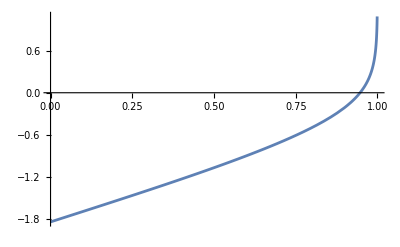

```mathematica
Plot[Limit[x+1/2 (-3-Log[2])+1/2 (-1/2 Log[1-x]+1/2 Log[1+x]),x->x1],{x1,0,1}]
```